```mathematica
rawdata=Import["/Users/stevenschowalter/Desktop/phys191mms/Rb Data/428fstep6.txt","Data"];
```

```mathematica
num=Dimensions[rawdata][[1]]
```

80

```mathematica
freq=Take[rawdata,All,{1}];
signal=Take[rawdata,All,{2}];
```

```mathematica
plotdata=Take[rawdata,All,2];
```

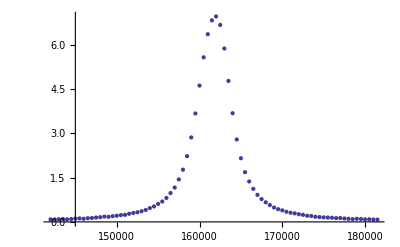

```mathematica
dataplot=ListPlot[plotdata]
```

```mathematica
Do[If[Max[signal]==signal[[i]][[1]],{Print[i,plotdata[[i]]],{max}=freq[[i]]}],{i,1,num}]
```

41{162000.,6.957}

```mathematica
model=g/(π (g^2+(x-x0)^2/b));
```

```mathematica
Needs["NonlinearRegression`"]
```

```mathematica
fitdata=NonlinearRegress[plotdata,model,{x0,g,b},x,MaxIterations->1000]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{4.51936×10^-17, -1.66853×10^-12, -1.66853×10^-12}, « 1 », {0., 0., -« 23 »}} may contain significant numerical errors.

{BestFitParameters→{x0→6.31431×10^6,g→83.3221,b→83.3221},ParameterCITable→ | Estimate | Asymptotic SE | CI
x0 | 6.31431×10^6 | 8.13537×10^21 | {-1.61996×10^22,1.61996×10^22}
g | 83.3221 | 7.20951×10^24 | {-1.4356×10^25,1.4356×10^25}
b | 83.3221 | 7.20951×10^24 | {-1.4356×10^25,1.4356×10^25},EstimatedVariance→4.70234,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 3 | 1.05024×10^-8 | 3.5008×10^-9
Error | 77 | 362.08 | 4.70234
Uncorrected Total | 80 | 362.08 | 
Corrected Total | 79 | 260.941 | ,AsymptoticCorrelationMatrix→(1. | -1. | 1.
-1. | 1. | -1.
1. | -1. | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 1.91207×10^21
Max Parameter-Effects | 6.22027×10^36
95. % Confidence Region | 0.605967}

```mathematica
fit=model/.fitdata[[1]][[2]];
```

```mathematica
fitplot=Plot[fit,{x,100000,200000},PlotStyle->{Red, Thick}];
```

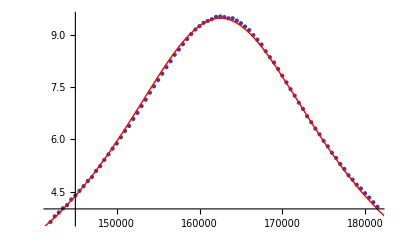

```mathematica
Show[dataplot,fitplot]
```